Here is our system of equations, with three compartments (S, I, and R) for each genotype.

```mathematica
I0'[t_,I0_,I1_,I2_,S0_,μ_,β0_,r_] := -r*I0[t]-μ*I0[t]+S0[t]*β0*(I0[t]+I1[t]+I2[t])
I1'[t_,I0_,I1_,I2_,S1_,μ_,β1_,r_] := -r*I1[t]-μ*I1[t]+S1[t]*β1*(I0[t]+I1[t]+I2[t])
I2'[t_,I0_,I1_,I2_,S2_,μ_,β2_,r_] := -r*I2[t]-μ*I2[t]+S2[t]*β2*(I0[t]+I1[t]+I2[t])

S0'[t_,I0_,I1_,I2_,S0_,μ_,β0_,r_,B_]:=-S0[t]*β0*(I0[t]+I1[t]+I2[t])
S1'[t_,I0_,I1_,I2_,S1_,μ_,β1_,r_,B_]:=-S1[t]*β1*(I0[t]+I1[t]+I2[t])
S2'[t_,I0_,I1_,I2_,S2_,μ_,β2_,r_,B_]:=-S2[t]*β2*(I0[t]+I1[t]+I2[t])

R0'[t_,I0_,I1_,I2_,S0_,μ0_,β0_,r0_]:=(r0+μ0)*I0[t]
R1'[t_,I0_,I1_,I2_,S1_,μ1_,β1_,r1_]:=(r1+μ1)*I1[t]
R2'[t_,I0_,I1_,I2_,S2_,μ2_,β2_,r2_]:=(r2+μ2)*I2[t]
```

First we need to solve to S0, S1, and S2 as a function of R (because we cannot, to my knowledge, solve them as a function of t). Letting R = R0+R1+R2 and dividing the S and R equations, we have:

```mathematica
Clear[μ,β0,β1,β2,r1,r2,r0,μ0,μ1,μ2,s0,NN,Λ]
```

```mathematica
DSolve[S0'[R] == (-β0 S0[R])/(r0+μ0), {S0},R]
DSolve[S1'[R] == (-β1 S1[R])/(r1+μ1), {S1},R]
DSolve[S2'[R] == (-β2 S2[R])/(r2+μ2), {S2},R]
```

{{S0→Function[{R},ⅇ^(-(R β0)/(r0+μ0)) C[1]]}}

{{S1→Function[{R},ⅇ^(-(R β1)/(r1+μ1)) C[1]]}}

{{S2→Function[{R},ⅇ^(-(R β2)/(r2+μ2)) C[1]]}}

Since there are no births in this system, we have S0, S1, and S2 corresponding to the disease-free equilibria (I=0 at the end of the epidemic, disease is not endemic). Let’s suppose that the initial frequency of S0 is s0, and the final value of r (i.e., individuals in the recovered class) is rf (note that here the ‘recovered’ class includes dead individuals). Then, using HW equilibrium, we have the following expression representing the total susceptible population after an epidemic.

```mathematica
FullSimplify[NN (s0*ⅇ^(-(rf β0)/(r0+μ0)) +2*(Sqrt[s0])*(1-Sqrt[s0])*ⅇ^(-(rf β1)/(r1+μ1)) +(1-Sqrt[s0])^2*ⅇ^(-(rf β2)/(r2+μ2)))]
```

NN (ⅇ^(-(rf β2)/(r2+μ2)) (-1+√s0)^2+ⅇ^(-(rf β1)/(r1+μ1)) (2 √s0-2 s0)+ⅇ^(-(rf β0)/(r0+μ0)) s0)

Let’s now attempt to solve for rf, the final number of ‘recovered’ individuals

```mathematica
Solve[NN-rf ==NN(ⅇ^(-(rf β2)/(r2+μ2)) (-1+√s0)^2+ⅇ^(-(rf β1)/(r1+μ1)) (2 √s0-2 s0)+ⅇ^(-(rf β0)/(r0+μ0)) s0),rf]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[NN-rf==NN (ⅇ^(-(rf β2)/(r2+μ2)) (-1+√s0)^2+ⅇ^(-(rf β1)/(r1+μ1)) (2 √s0-2 s0)+ⅇ^(-(rf β0)/(r0+μ0)) s0),rf]

Doh. No solution for that one. But! We can note that we can solve this when (β/(r+μ)) is a constant. Let β/(r+μ) = Λ. Then we have:

```mathematica
ClearAll[NN,Λ,s0,rf]
```

```mathematica
FullSimplify[NN( s0*ⅇ^(-rf Λ) +2*(Sqrt[s0])*(1-Sqrt[s0])ⅇ^(-rf Λ) +(1-Sqrt[s0])^2*ⅇ^(-rf Λ) )]
```

ⅇ^(-rf Λ) NN

```mathematica
FullSimplify[Solve[NN-rf==NN ⅇ^(-rf Λ) , rf]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rf→NN+ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ}}

```mathematica
rf[Λ_,NN_]:=NN+ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ
```

```mathematica
rf[1/(2+0.05),1000]
```

General::munfl: Internal`AbsSquare[-6.87511×10^-210] is too small to represent as a normalized machine number; precision may be lost.

1000.

Now we have rf, which means we can compare the number of individuals within each genotype class. We need to additionally adjust for the number of individuals who recovered and survived within each class.

```mathematica
ClearAll[a1Final,β,r0,r1,r2,μ0,μ1,μ2,μ,r,Λ,s0,NN,s0]

S0Final[NN_,Λ_,s0_]:=NN s0*ⅇ^(-rf[Λ,NN] Λ)
S1Final[NN_,Λ_,s0_]:=NN 2*(Sqrt[s0])*(1-Sqrt[s0])*ⅇ^(-rf[Λ,NN]Λ)
S2Final[NN_,Λ_,s0_]:=NN((1-Sqrt[s0])^2)*ⅇ^(-rf [Λ,NN]Λ)

R0Final[NN_,Λ_,s0_,r0_,μ0_]:=(s0 NN-S0Final[NN,Λ,s0])*r0/(r0+μ0)
R1Final[NN_,Λ_,s0_,r1_,μ1_]:=( 2*(Sqrt[s0])*(1-Sqrt[s0])NN-S1Final[NN,Λ,s0])*r1/(r1+μ1)
R2Final[NN_,Λ_,s0_,r2_,μ2_]:=(NN(1-Sqrt[s0])^2-S2Final[NN,Λ,s0])*r2/(r2+μ2)
```

```mathematica
Nf[NN_,Λ_,s0_,r0_,μ0_,r1_,μ1_,r2_,μ2_]:=(S0Final[NN,Λ,s0]+S1Final[NN,Λ,s0]+S2Final[NN,Λ,s0]+R0Final[NN,Λ,s0,r0,μ0]+R1Final[NN,Λ,s0,r1,μ1]+R2Final[NN,Λ,s0,r2,μ2])
```

```mathematica
Nf[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]
```

ⅇ^(Λ (-NN-ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ)) NN (1-√s0)^2+2 ⅇ^(Λ (-NN-ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ)) NN (1-√s0) √s0+ⅇ^(Λ (-NN-ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ)) NN s0+(r0 (NN s0-ⅇ^(Λ (-NN-ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ)) NN s0))/(r0+μ0)+(r1 (2 NN (1-√s0) √s0-2 ⅇ^(Λ (-NN-ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ)) NN (1-√s0) √s0))/(r1+μ1)+(r2 (NN (1-√s0)^2-ⅇ^(Λ (-NN-ProductLog[-ⅇ^(-NN Λ) NN Λ]/Λ)) NN (1-√s0)^2))/(r2+μ2)

```mathematica
G0Final[NN_,Λ_,s0_,r0_,μ0_,r1_,μ1_,r2_,μ2_]:=(S0Final[NN,Λ,s0]+R0Final[NN,Λ,s0,r0,μ0])/Nf[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]

G1Final[NN_,Λ_,s0_,r0_,μ0_,r1_,μ1_,r2_,μ2_]:=(S1Final[NN,Λ,s0]+R1Final[NN,Λ,s0,r1,μ1])/Nf[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]

G2Final[NN_,Λ_,s0_,r0_,μ0_,r1_,μ1_,r2_,μ2_]:=(S2Final[NN,Λ,s0]+R2Final[NN,Λ,s0,r2,μ2])/Nf[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]
```

```mathematica
β=1;
NN=1000;
r0 = 0.05;
μ0 = 2;
r1 = 02;
μ1  = 0.05;
r2 = 2;
μ2  = 0.05;
Λ = β/(r0+μ0);
```

```mathematica
G0Final[1000,Λ,0.1,r0,μ0,r1,μ1,r2,μ2]
```

General::munfl: Internal`AbsSquare[-6.87511×10^-210] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.00277008

```mathematica
G1Final[1000,Λ,0.1,r0,μ0,r1,μ1,r2,μ2]
```

General::munfl: Internal`AbsSquare[-6.87511×10^-210] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.479175

```mathematica
G2Final[1000,Λ,0.1,r0,μ0,r1,μ1,r2,μ2]
```

General::munfl: Internal`AbsSquare[-6.87511×10^-210] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.518055

```mathematica
FullSimplify[G0Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]]
```

(ⅇ^(NN Λ+ProductLog[-ⅇ^(-NN Λ) NN Λ]) s0 (r1+μ1) (r2+μ2) (r0-(μ0 ProductLog[-ⅇ^(-NN Λ) NN Λ])/(NN Λ)))/(r1 r2 s0 μ0+r1 (r0 (-1+√s0)^2+μ0-2 √s0 μ0+2 s0 μ0) μ2+μ0 μ1 (2 r2 √s0-r2 s0+μ2)+r0 μ1 (2 r2 √s0-2 r2 s0+μ2-s0 μ2)+ⅇ^(NN Λ+ProductLog[-ⅇ^(-NN Λ) NN Λ]) (r2 (-1+√s0)^2 μ0 μ1+r1 μ0 (r2-r2 s0+2 √s0 μ2-2 s0 μ2)+r0 r1 (r2+2 √s0 μ2-s0 μ2)+r0 μ1 (r2-2 r2 √s0+2 r2 s0+s0 μ2)))

```mathematica
FullSimplify[G1Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]]
```

-((2 (-1+√s0) √s0 (r0+μ0) (r2+μ2) (NN r1 Λ-μ1 ProductLog[-ⅇ^(-NN Λ) NN Λ]))/(NN Λ (r2 (-1+√s0)^2 μ0 μ1+r1 μ0 (r2-r2 s0+2 √s0 μ2-2 s0 μ2)+r0 r1 (r2+2 √s0 μ2-s0 μ2)+r0 μ1 (r2-2 r2 √s0+2 r2 s0+s0 μ2))-(r1 r2 s0 μ0+r1 (r0 (-1+√s0)^2+μ0-2 √s0 μ0+2 s0 μ0) μ2+μ0 μ1 (2 r2 √s0-r2 s0+μ2)+r0 μ1 (2 r2 √s0-2 r2 s0+μ2-s0 μ2)) ProductLog[-ⅇ^(-NN Λ) NN Λ]))

```mathematica
FullSimplify[G2Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]]
```

-(((-1+√s0)^2 (r0+μ0) (r1+μ1) (NN r2 Λ-μ2 ProductLog[-ⅇ^(-NN Λ) NN Λ]))/(-NN Λ (r2 (-1+√s0)^2 μ0 μ1+r1 μ0 (r2-r2 s0+2 √s0 μ2-2 s0 μ2)+r0 r1 (r2+2 √s0 μ2-s0 μ2)+r0 μ1 (r2-2 r2 √s0+2 r2 s0+s0 μ2))+(r1 r2 s0 μ0+r1 (r0 (-1+√s0)^2+μ0-2 √s0 μ0+2 s0 μ0) μ2+μ0 μ1 (2 r2 √s0-r2 s0+μ2)+r0 μ1 (2 r2 √s0-2 r2 s0+μ2-s0 μ2)) ProductLog[-ⅇ^(-NN Λ) NN Λ]))

```mathematica
(*g0Final[NN_,Λ_,s0_,r0_,μ0_]:=s0*(ⅇ^(-rf[Λ,NN] Λ)+(1-ⅇ^(-rf[Λ,NN] Λ))*(r0/(r0+μ0)))
g1Final[NN_,Λ_,s0_,r1_,μ1_]:=2*(Sqrt[s0])*(1-Sqrt[s0])*(ⅇ^(-rf[Λ,NN]Λ)+(1-ⅇ^(-rf[Λ,NN]Λ))*(r1/(r1+μ1)))
g2Final[NN_,Λ_,s0_,r2_,μ2_]:=((1-Sqrt[s0])^2)*(ⅇ^(-rf [Λ,NN]Λ)+(1-ⅇ^(-rf [Λ,NN]Λ))*(r2/(r2+μ2)))*)
```

Now, Allele frequencies :

```mathematica
ClearAll[a1Final,β,r0,r1,r2,μ0,μ1,μ2,μ,r,Λ]
```

```mathematica
a1Final[NN_,Λ_,s0_,r0_,μ0_,r1_,μ1_,r2_,μ2_]:=(G0Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]+(1/2)*G1Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2])
```

```mathematica
a2Final[NN_,Λ_,s0_,r0_,μ0_,r1_,μ1_,r2_,μ2_]:=1-a1Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]
```

```mathematica
Clear[Λ,s0,r0,μ0,r1,μ1,r2,μ2]
FullSimplify[a2Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]]
```

```mathematica
-(((-1+√s0) (r0+μ0) (r2 √s0 μ1+(r1-r1 √s0+μ1) μ2+ⅇ^(NN Λ+ProductLog[-ⅇ^(-NN Λ) NN Λ]) (r2 (r1+μ1-√s0 μ1)+r1 √s0 μ2)))




/(r1 r2 s0 μ0+r1 (r0 (-1+√s0)^2+μ0-2 √s0 μ0+2 s0 μ0) μ2+μ0 μ1 (2 r2 √s0-r2 s0+μ2)+r0 μ1 (2 r2 √s0-2 r2 s0+μ2-s0 μ2)+ⅇ^(NN Λ+ProductLog[-ⅇ^(-NN Λ) NN Λ]) (r2 (-1+√s0)^2 μ0 μ1+r1 μ0 (r2-r2 s0+2 √s0 μ2-2 s0 μ2)+r0 r1 (r2+2 √s0 μ2-s0 μ2)+r0 μ1 (r2-2 r2 √s0+2 r2 s0+s0 μ2))))
```

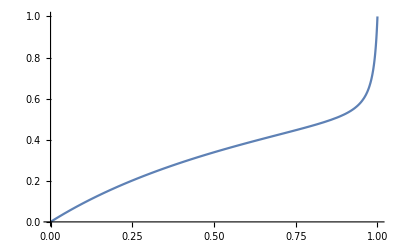

```mathematica
β=1;
NN=100;
r0 = 0.05;
μ0 = 2;
r1 = 02;
μ1  = 0.05;
r2 = 2;
μ2  = 0.05;
Λ = β/(r0+μ0);

plB=Plot[{a1Final[NN,Λ,x0^2,r0,μ0,r1,μ1,r2,μ2]},{x0,0,1}]
```

```mathematica
(*need to fix scaling on Beta between theory and *)
```

```mathematica
Vals={};
xVals={};
For[s0=0.01,s0<1,s0=s0+0.01,
{
ClearAll[β0,β1,β2,I0,I1,I2,R0,R1,R2,S0,S1,S2];
p=s0^0.5;
q=1-p;
β0=1;
β1=1;
β2=1;
NN=10^3;

{sol=NDSolve[{I0'[t] == -r0*I0[t]-μ0*I0[t]+S0[t]*β0*(I0[t]+I1[t]+I2[t]),
I1'[t] == -r1*I1[t]-μ1*I1[t]+S1[t]*β1*(I0[t]+I1[t]+I2[t]),
I2'[t] == -r2*I2[t]-μ2*I2[t]+S2[t]*β2*(I0[t]+I1[t]+I2[t]),
S0'[t]==-S0[t]*β0*(I0[t]+I1[t]+I2[t]),
S1'[t]==-S1[t]*β1*(I0[t]+I1[t]+I2[t]),
S2'[t]==-S2[t]*β2*(I0[t]+I1[t]+I2[t]),
R0'[t]==(r0)*I0[t],
R1'[t]==(r1)*I1[t],
R2'[t]==(r2)*I2[t],R0[0] == 0,R1[0]==0,R2[0] == 0, S0[0]== s0*NN,S1[0]==2*p*q*NN-0.001,S2[0]==(q^2)*NN,I0[0]==0.00,I2[0]==0.00,I1[0]==0.001},{R0,S0,I0,R1,S1,R2,S2},{t,0,1000}];Vals=Append[Vals,(Part[S0[1000]/.sol,1]+Part[R0[1000]/.sol,1]+0.5*(Part[S1[1000]/.sol,1]+Part[R1[1000]/.sol,1]))/(Part[S0[1000]/.sol,1]+Part[R0[1000]/.sol,1]+Part[S1[1000]/.sol,1]+Part[R1[1000]/.sol,1]+Part[S2[1000]/.sol,1]+Part[R2[1000]/.sol,1])];xVals=Append[xVals,s0]}
}]
```

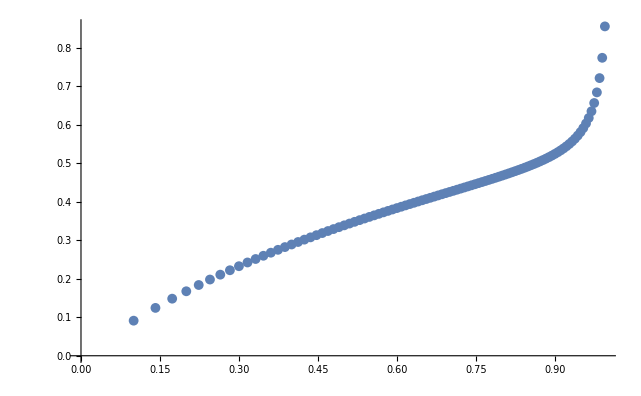

```mathematica
plA=ListPlot[Transpose[{(xVals)^0.5,Vals}]]
```

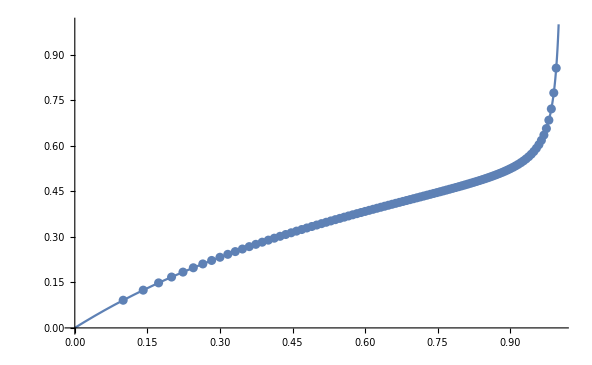

```mathematica
Show[plB,plA]
```

We model the change in allele frequency of a selected allele as:

```mathematica
ClearAll[x,NN,s,Λ,s0,r0,μ0,r1,μ1,r2,μ2]
P[x_,NN_,s_]:= (1-e^(-4 NN s x))/(1-e^(-4 NN s ))
```

```mathematica
FullSimplify[P[xf,NN,s]-P[x0,NN,s]]
```

(e^(4 NN s) (e^(-4 NN s x0)-e^(-4 NN s xf)))/(-1+e^(4 NN s))

```mathematica
Integrate[P[xf,NN,s]-P[x0,NN,s],{x0,0,1}]
```

-e^(-4 NN s (-1+xf))/(-1+e^(4 NN s))+1/(4 NN s Log[e])

```mathematica
FullSimplify[a1Final[NN,Λ,s0,r0,μ0,r1,μ1,r2,μ2]]
```

((r1 s0 μ0+√s0 (r0-r0 √s0+μ0) μ1+ⅇ^(NN Λ+ProductLog[-ⅇ^(-NN Λ) NN Λ]) (r1 √s0 (r0+μ0-√s0 μ0)+r0 s0 μ1)) (r2+μ2))/(r1 r2 s0 μ0+r1 (r0 (-1+√s0)^2+μ0-2 √s0 μ0+2 s0 μ0) μ2+μ0 μ1 (2 r2 √s0-r2 s0+μ2)+r0 μ1 (2 r2 √s0-2 r2 s0+μ2-s0 μ2)+ⅇ^(NN Λ+ProductLog[-ⅇ^(-NN Λ) NN Λ]) (r2 (-1+√s0)^2 μ0 μ1+r1 μ0 (r2-r2 s0+2 √s0 μ2-2 s0 μ2)+r0 r1 (r2+2 √s0 μ2-s0 μ2)+r0 μ1 (r2-2 r2 √s0+2 r2 s0+s0 μ2)))

```mathematica
(1-x0)^2
```

```mathematica
SFS[x_,s_,NN_]:=ⅇ^(4NN s)(1-ⅇ^(-4 NN s(1-x)))/((ⅇ^(4 NN s)-1)x(1-x))
```

```mathematica
Clear[NN]
```

```mathematica
(*It's (1-x0)^2 below because of the way we defined s0 -- s0 corresponds to the ancestral allele, or 0 copies of the effect allele).
```

```mathematica
Integrate[SFS[x0,s,NN](P[a1Final[NN,Λ,(1-x0)^2,r0,μ0,r1,μ1,r2,μ2],NN,s]-P[x0,NN,s]),{x0,0,1}]
```

∫_0^1 1/((-1+ⅇ^(4 NN s)) (1-x0) x0)(1/(1-e^(-4 NN s))(1-e^(-4 NN s ((0.0243902 (NN (1-x0)^2-ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-x0)^2)+ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-x0)^2)/(0.97561 (NN (1-√((1-x0)^2))^2-ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2))^2)+0.0243902 (NN (1-x0)^2-ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-x0)^2)+ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2))^2+0.97561 (2 NN (1-√((1-x0)^2)) √((1-x0)^2)-2 ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2)) √((1-x0)^2))+ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-x0)^2+2 ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2)) √((1-x0)^2))+(0.97561 (2 NN (1-√((1-x0)^2)) √((1-x0)^2)-2 ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2)) √((1-x0)^2))+2 ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2)) √((1-x0)^2))/(2 (0.97561 (NN (1-√((1-x0)^2))^2-ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2))^2)+0.0243902 (NN (1-x0)^2-ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-x0)^2)+ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2))^2+0.97561 (2 NN (1-√((1-x0)^2)) √((1-x0)^2)-2 ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2)) √((1-x0)^2))+ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-x0)^2+2 ⅇ^(0.487805 (-NN-2.05 ProductLog[-0.487805 ⅇ^(-0.487805 NN) NN])) NN (1-√((1-x0)^2)) √((1-x0)^2))))))-(1-e^(-4 NN s x0))/(1-e^(-4 NN s))) ⅇ^(4 NN s) (1-ⅇ^(-4 NN s (1-x0)))ⅆx0

## Figures

Figure 1 will be a concept figure, outlining the evolutionary and epi models. Also need to include a panel with the tradeoffs.

Figure 2 will be a demonstration of the epi effects on allele frequency. Panel A will be a timecourse of frequency change within a single epidemic . Panel B will be the shift in allele frequency spectrum expected for a given set of parameters, as compared to the SFS in the absence of epidemics.

```mathematica
s0=0.1;
ClearAll[β0,β1,β2,r0,r1,r2,μ1,μ2,μ0,I0,I1,I2,R0,R1,R2,S0,S1,S2];
p=s0^0.5;
q=1-p;
β0=0.1;
β1= 0.1;
β2 = 0.1;
NN=1000;
r0 = 0.1;
μ0 = 0.05;
r1 = 0.1;
μ1  = 0.05;
r2 = 0.1;
μ2  = 0.05;

sol=NDSolve[{I0'[t] == -r0*I0[t]-μ0*I0[t]+S0[t]*β0*(I0[t]+I1[t]+I2[t]),
I1'[t] == -r1*I1[t]-μ1*I1[t]+S1[t]*β1*(I0[t]+I1[t]+I2[t]),
I2'[t] == -r2*I2[t]-μ2*I2[t]+S2[t]*β2*(I0[t]+I1[t]+I2[t]),
S0'[t]==-S0[t]*β0*(I0[t]+I1[t]+I2[t]),
S1'[t]==-S1[t]*β1*(I0[t]+I1[t]+I2[t]),
S2'[t]==-S2[t]*β2*(I0[t]+I1[t]+I2[t]),
R0'[t]==(r0)*I0[t],
R1'[t]==(r1)*I1[t],
R2'[t]==(r2)*I2[t],R0[0] == 0,R1[0]==0,R2[0] == 0, S0[0]== s0*NN,S1[0]==2*p*q*NN-0.001,S2[0]==(q^2)*NN,I0[0]==0.00,I2[0]==0.00,I1[0]==0.1},{R0,S0,I0,R1,S1,R2,S2},{t,0,1000}];
```

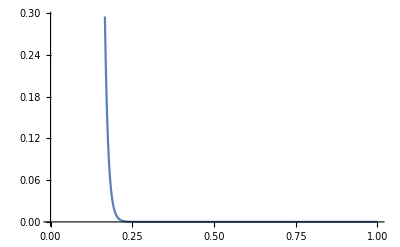

```mathematica
Plot[S2[t]/.sol,{t,0,1}]
```

Figure 3 will be a) rate of fixation for different tradeoff models and b) alpha for different tradeoff models.

Figure 4 will be effect of N on fixation rates . Could be interesting given joint effects of density dependence and drift.

Figure 5 will be Empirical data.

Allele Frequency Dynamics for One Epidemic